# A Systematic Approach to Combinatorics Word Problems with the Twelve Fold Way

Peter Cullen Burbery

Many combinatorics word problems can be organized according to a system known as the twelve fold way. I created a function to compute a table for the twelve fold way. I also discuss an expanded version named the twenty fold way.

## What is the twelve-fold way?

In combinatorics, the twelvefold way is a systematic classification of 12 related enumerative problems concerning two finite sets, which include the classical problems of counting permutations, combinations, multisets, and partitions either of a set or of a number.

The twelve fold way has applications to word problems. I am going to generate some with a function I created.

```mathematica
CombinatoricsQuestionGenerator[<|"n"->5,"k"->7,"N"->"balls","K"->"boxes","distinct"->"distinct","orbit"->"indistinct"|>]//TableForm
```

|  | 
 |  | 
 |  | 
 |  |

To find the answers, I will translate the problem to abstract mathematical concepts to get numerical answers, and then relate the abstract output to the word problem I asked.

## Abstraction

Let N and X be finite sets. Let n be the cardinality or number of elements or length of N and x be the cardinality of X. Then N is an n-set and X is an x-set. For example if N is {1,2} then N is a 2-set and if X is {1,2,3} then X is a 3-set.

I can evaluate the cardinality with Length and generate a set with Range.

```mathematica
Range[57]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57}

```mathematica
Length[Range[57]]
```

57

## Function

In mathematics, a function from a set X to a set R assigns each element of X exactly one element of R. The set X is called the domain of the function and set R is called the codomain of the function.

A function

The general problem we consider is the enumeration of equivalence classes of functions f:N↦X.

The functions are subject to one of the following restrictions:

No condition: each b in N may be sent by f to any c in X, and each c may occur multiple times.

f is injective: each value f(b) for b in N must be distinct from every other b. There cannot be more than one b of X in the image of f.

I can evaluate if a function is injective with FunctionInjective.

```mathematica
FunctionInjective[Log[x],x]
```

True

```mathematica
FunctionInjective[Sin[x],x]
```

False

This is an example of an injective function. This is also called a one-to-one function.

This is an example of a function that is not injective.

Here is another example of a function that is not injective.

f is surjective: each value f(b) for b in N must be distinct from every other b. There cannot be more than one b of X in the image of f.

I can evaluate if a function is surjective with Function Surjective.

```mathematica
FunctionSurjective[Tan[x],x]
```

True

This is an example of a surjective function. This is also known as an onto function.

This is an example of a function that is not surjective:

If a function is surjective and injective it is bijective. This is an example of a bijective function. A bijective function is also referred to as an invertible function.

This is an example of a function is that not surjective or injective:

Here are all four types:

□ | Surjective/onto | non-surjective
Injective
one to one
invertible | -Graphics- | -Graphics-
non-injective | -Graphics- | -Graphics-

Here is a four illustrations:

□ | Surjective/onto | non-surjective
Injective
one to one
invertible | ℝ->ℝ:x↦x
->:x↦x^2 and its inverse
->:x↦√x
ℝ->:x↦ⅇ^x with its 
codomain restricted
to its image
and its inverse
->ℝ:x↦ln x | ℝ->ℝ:x↦ⅇ^x 
non-injective | ℝ->ℝ:x↦(x-1)x(x+1) or
ℝ->ℝ:x↦x^3-x
ℝ->[-1,1]:x↦sin(x) | ℝ->ℝ:x↦sin(x)

Notice that the function's domain and codomain determines whether it is surjective and injective. For example when the codomain is positive reals, the exponential function ⅇ^x is bijective but the function is only injective when the codomain is the entire set of real numbers. Sine is surjective if its codomain is the closed interval [-1,1] but if its codomain is the reals, its not injective or surjective.

The codomain for sine when it is surjective.

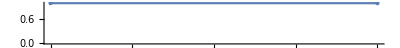

```mathematica
NumberLinePlot[Interval[{-1,1}]]
```

In category theory, injections, surjections, and bijections correspond precisely to monomorphisms, epimorphisms, and isomorphisms, respectively.

The image of a function is the set of outputs the function produces.

```mathematica
CatalanNumber[5]
```

42

```mathematica
CatalanNumber[3]
```

5

1.

Here's the abstract table:

The twelve combinatorial objects and their enumeration formulas |  |  | 
f-class | Any f | Injective f | Surjective f
Distinct f | n-sequence in X
x^n | n-permutation of X | composition of N with x subsets
x!{x
n}
S_n orbits
f∘S_n | n-multisubset of X
(x+n-1
n) | n-subset of X
(x
n) | composition of n with x terms
(n-1
n-x)
S_x orbits
S_x∘f | partition of N into ≤x subsets
∑_(k=0)^x {x+n-1
n} | partition of N into <=x elements
[n<=x] | partition of N into x subsets
{x
n}
S_n×S_x
orbits
S_x∘f∘S_n | partition of n into <=x parts
p_x(n+x) | partition of n into <=x parts
1
[n<=x] | partition of n into x parts
p_x(n)

I'm going